## Panel Plot Varying TempThresh and Omega

### Set up data

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/export_data"];
```

```mathematica
dataOmega={Import["series_data/sim_omega_1.dat"],
Import["series_data/sim_omega_1p5.dat"],
Import["series_data/sim_omega_3.dat"],
Import["series_data/sim_omega_10.dat"]};

dataTempThresh={Import["series_data/sim_tempThresh_2.dat"],
Import["series_data/sim_tempThresh_2p5.dat"],
Import["series_data/sim_tempThresh_3.dat"]};
```

```mathematica
(* baseline parameters are

x0=0.05; (* proportion of mitigators in 2010 *)
κ=0.05;
δ=1;
β=1;

(* temp prediction (linear extrapolation from previous temperatures) *) 
tempProjOnOff=1; (* on 1, off 0 *)
deltat=50; (* years looking ahead *)

*)
```

```mathematica
(* time ticks *)
timeTicks=Table[{50(i-1),1800+50(i-1)},{i,1,13}];

(* imgs size *)
imgs=325;
(* aspect ratio *)
aratio=0.6;
(* legend position (scaled) *)
legendPos={0.2,0.5};
(* labels (alphabet) *)
labels=Alphabet[];
(* label position (scaled) *)
labelPos={0.05,0.91};
(* bold label on off *)
bold=1;
```

```mathematica
{padLeft,padRight,padBottom,padTop}={50,30,40,20};  (* image padding *)
```

```mathematica
(* time plot range *)
plRange={100,400};
(* social plot range *)
plRangeSoc={-0.02,1.05};
(* emissions plot range *)
plRangeEm={-0.5,18.5};
(* temperature plot range *)
plRangeTemp={-0.1,5.3};
```

```mathematica
(* varying parameter values *)
omegaVals={1,1.5,3,10};
tempThreshVals={2,2.5,3};
```

```mathematica
(* plots to keep *)
plotNumsOmega={1,2,3,4};
plotNumsTempThresh={1,2,3};
```

```mathematica
tVals=Table[i,{i,0,1200}];
```

```mathematica
legendOmega=LineLegend[Table[TMBcolours[[i]],{i,Length[plotNumsOmega]}],Table["ω ="<>ToString[omegaVals[[i]]],{i,plotNumsOmega}]]

legendTempThresh=LineLegend[Table[TMBcolours[[i]],{i,Length[plotNumsTempThresh]}],Table["T_c ="<>ToString[tempThreshVals[[i]]],{i,plotNumsTempThresh}]];
```

```mathematica
aratio
```

0.6

### omega Plots

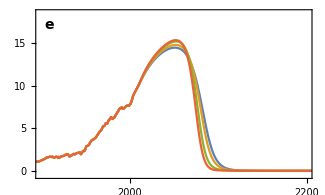

```mathematica
(* emissions plot omega *)
emissionPlotOmega=ListLinePlot[Table[Transpose[{tVals,dataOmega[[j,1]]}],{j,plotNumsOmega}],
PlotRange->{plRange,plRangeEm},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameLabel->{{None,None},{None,None}},
Epilog->Text[Style[labels[[5]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

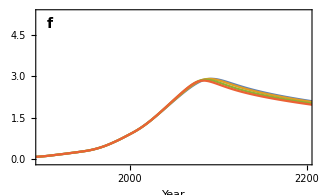

```mathematica
(* temp plot omega *)
tempPlotOmega=ListLinePlot[Table[Transpose[{tVals,dataOmega[[j,2]]}],{j,plotNumsOmega}],
PlotRange->{plRange,plRangeTemp},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
(*PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]]*)
FrameLabel->{{None,None},{"Year",None}},
Epilog->Text[Style[labels[[6]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

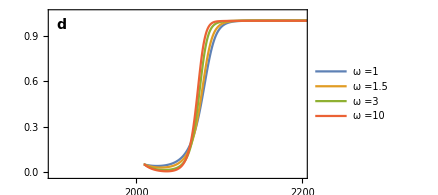

```mathematica
(* social plot omega *)
socPlotOmega=ListLinePlot[Table[Transpose[{tVals[[210;;]],dataOmega[[j,4,210;;]]}],{j,plotNumsOmega}],
PlotRange->{plRange,plRangeSoc},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
PlotLegends->Placed[legendOmega,Scaled[legendPos]],
FrameLabel->{{None,None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[4]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

### tempThresh Plots

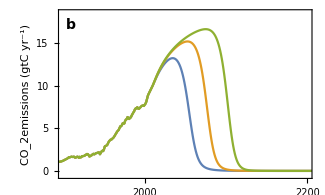

```mathematica
(* emissions plot omega *)
emissionPlotTempThresh=ListLinePlot[Table[Transpose[{tVals,dataTempThresh[[j,1]]}],{j,plotNumsTempThresh}],
PlotRange->{plRange,plRangeEm},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[2]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

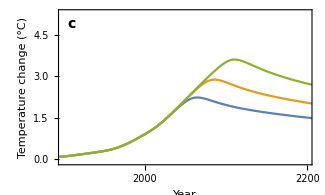

```mathematica
(* temp plot omega *)
tempPlotTempThresh=ListLinePlot[Table[Transpose[{tVals,dataTempThresh[[j,2]]}],{j,plotNumsTempThresh}],
PlotRange->{plRange,plRangeTemp},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
(*PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]]*)
FrameLabel->{{"Temperature change (°C)",None},{"Year",None}},
Epilog->Text[Style[labels[[3]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

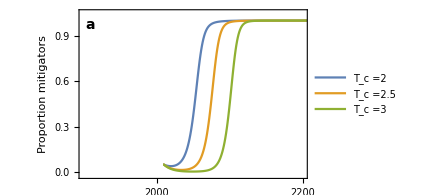

```mathematica
(* social plot omega *)
socPlotTempThresh=ListLinePlot[Table[Transpose[{tVals[[210;;]],dataTempThresh[[j,4,210;;]]}],{j,plotNumsTempThresh}],
PlotRange->{plRange,plRangeSoc},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
PlotLegends->Placed[legendTempThresh,Scaled[legendPos]],
FrameLabel->{{"Proportion mitigators",None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[1]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

### Plot Grid

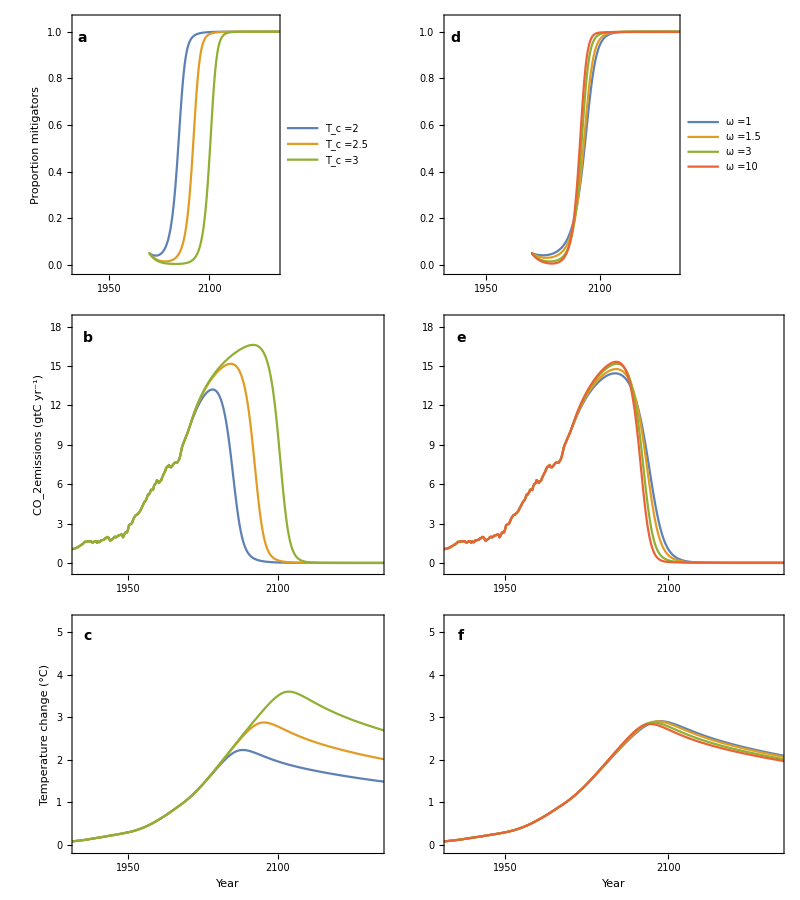

```mathematica
plotGrid=Grid[{{socPlotTempThresh,socPlotOmega},{emissionPlotTempThresh,emissionPlotOmega},{tempPlotTempThresh,tempPlotOmega}},Spacings->{-2.5,-2.2}]
```

```mathematica
Export["../figures/grid_tempThresh_omega.png",plotGrid,ImageResolution->100];
```